# Homework 12

Name: Muhammad Salah Shatla

ID: 201500059

## Problem 1

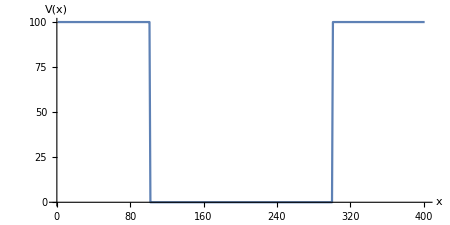

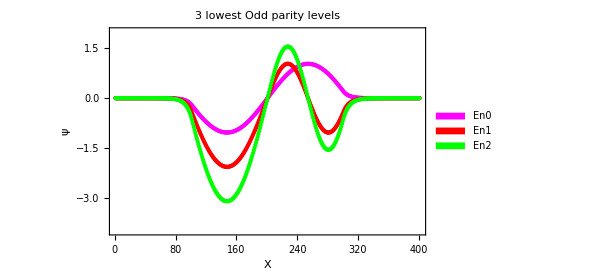

The exact Energies for the first 5 odd levels:
 {4.9348, 19.7392, 44.4132, 78.9568, 123.37}the estimated values using the shooting method were:
{4.33906, 4.33906, 4.33906, 4.33906, 4.33906}

session time = 2.976296

```mathematica
ClearAll["Global`*"]
t=SessionTime[];
xMax = 2.0; dx = 0.01; 
x = Range[-xMax, xMax, dx]; lx = Length[x];
v = Table[0.0, {i,lx}];
potEng = 100.0;
Do[
If[x[[i]]<= -1.0, v[[i]] = potEng];
If[x[[i]]>= 1.0, v[[i]] = potEng];
If[x[[i]]== 0.0,i0 = i]; (* i0 = central position of the well *)
,{i,lx}];
nEng = 5; (* number of energy levels *)
color={Magenta,Red,Green,Orange,Yellow};
labels={"En0","En1","En2","En3","En4"};
engOddList = Table[0.0, {i,nEng}];
plot = Table[0.0, {i,nEng}];

eng = 1.0; (* first guess for E *)
psiMax = 2.0; (* top bound for psi *)

Do[
dE = .4; (* first guess for dE *) 

(* Obtaining the sign of the initial psi RIGHT*)
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = -dx*j;  (* δx slop at x = 0 and 0.0 ψ at x=0*)
i=i0+1;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiLastR=psi[[i-1]] ; (* Last value of psi before quitting *)

While[Abs[dE] >0.000000000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = -dx*j; psi[[i0 +1]] = dx*j;  (* δx slop at x = 0 and 0.0 ψ at x=0*)


i=i0+2;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiNewR=psi[[i-1]] ;
If[Sign[psiNewR] == Sign[psiLastR], eng = eng + dE]; 
If[Sign[psiNewR] != Sign[psiLastR],dE=-dE/2.0; eng = eng + dE];
psiLastR = psiNewR];

dEl=0.4;
While[Abs[dEl] > 0.0000000001,
k=i0-2;
While[Abs[psi[[k+1]]] < psiMax && k > 0,
psi[[k]] = 2.0 psi[[k+1]] - psi[[k+2]] - 2.0 (eng - v[[k+1]])psi[[k+1]] dx^2;  k--];
psiNewL=psi[[k+1]] ;
If[Sign[psiNewL] == Sign[psiLastL], eng = eng - dEl]; (*used negative here to reverse direction*)
If[Sign[psiNewL] != Sign[psiLastL],dEl=-dEl/2.0; eng = eng + dEl];
psiLastL = psiNewL];


engOddList[[j]] = eng;
eng = eng + 0.5;



plot[[j]]=ListPlot[psi/0.328,PlotRange->All,PlotStyle->{color[[j]],PointSize->0.005},PlotLegends->SwatchLegend[{color[[j]]},{labels[[j]]}]]
,{j,nEng}];

(* Results *)
leg=SwatchLegend[{Red,Yellow,Orange},{"E0","E1","E2"}];
engOddList (* Calculations using shooting method *);
engExact =Table[((2.0n ) Pi/2.0)^2/2.0,{n,5}] ;
ListPlot[v, Joined->True, AxesLabel->{"x","V(x)"},AspectRatio->0.5,ImageSize->450]
Show[plot[[1]],plot[[2]],plot[[3]],PlotRange-> {-4,2},ImageSize->450,Frame -> True, FrameLabel->{Style["X",FontSize->15],Style["ψ",FontSize->20]},PlotLabel->"3 lowest Odd parity levels"]

Print["The exact Energies for the first 5 odd levels:\n " <>ToString [engExact]<>"the estimated values using the shooting method were:\n" <>ToString[engOddList]]

Print["session time = ",SessionTime[]-t]
```

## Problem 2

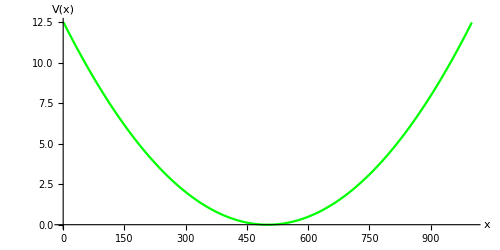

The exact Energies for the first 5 odd levels are:
 {0.5,1.5,2.5,3.5,4.5}
the estimated values using the shooting method were:
{0.499997, 1.49998, 2.49996, 3.49992, 4.49988}

session time = 14.367533

```mathematica
ClearAll["Global`*"]
t=SessionTime[];
xMax = 5.0; dx = 0.01; 
x = Range[-xMax, xMax, dx]; lx = Length[x];
v = Table[1/2 i^2, {i,-xMax,xMax,dx}];
i0 = 0 (* central position of the well *);

nEng = 5; (* number of energy levels *)
color={Red,Yellow,Orange,Green,Magenta};
labels={"En0","En1","En2","En3","En4"};
engList = Table[0.0, {i,nEng}];
plot = Table[0.0, {i,nEng}];

eng = 0.01; (* first guess for E *);
psiMax = 3.0; (* top bound for psi *)

Do[
dE = .004; (* first guess for dE *) 
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] = 0.0000000000000000000000000001; 
i=i0+1;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiLastR=psi[[i-1]] ; 


While[Abs[dE] >0.000000000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 -1]] =0.0000000000000000000000000001;

i=i0+1;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] - 2.0 (eng - v[[i-1]])psi[[i-1]] dx^2;  i++];
psiNewR=psi[[i-1]] ;
If[Sign[psiNewR] == Sign[psiLastR], eng = eng + dE]; 
If[Sign[psiNewR] != Sign[psiLastR],dE=-dE/2.0; eng = eng + dE];
psiLastR = psiNewR];

engList[[j]] = eng;
eng = eng + 0.001;
,{j,nEng}];
leg=SwatchLegend[{Red,Yellow,Orange},{"E0","E1","E2"}];
engList (* Calculations using shooting method *);
engExact =Table[((n-1.0)+1/2),{n,5}] //StandardForm;(* Exact .. since h=m=k=1*)
ListPlot[v, Joined->True, AxesLabel->{"x","V(x)"},AspectRatio->0.5,PlotStyle->Green,ImageSize->500]


Print["The exact Energies for the first 5 odd levels are:\n " <>ToString [engExact]<>"\nthe estimated values using the shooting method were:\n" <>ToString[engList]]

Print["session time = ",SessionTime[]-t]
```

## Problem 3

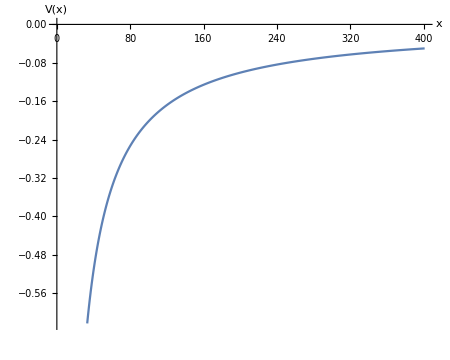

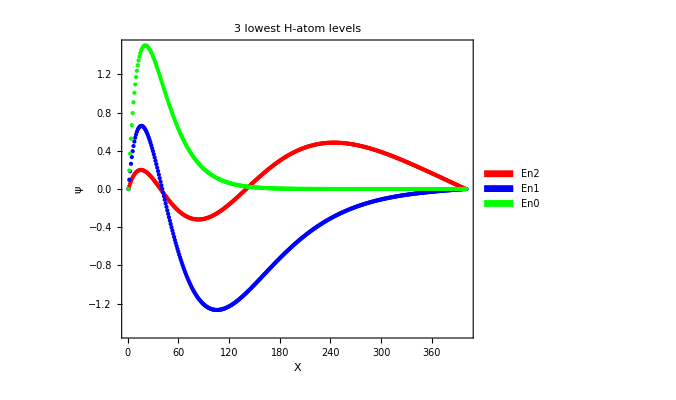

The exact Energies for the first 3 energy levels are:
 {-0.5,-0.125,-0.0555556}
the estimated values using the shooting method are:
{-0.499688, -0.124967, -0.0498172}

session time = 1.692031

```mathematica
ClearAll["Global`*"]
t=SessionTime[];
xMax = 20.0; dx =0.05; 
x = Range[0, xMax, dx]; lx = Length[x];
v = Table[-1/i, {i,0.0000000000000000001,xMax,dx}];
i0 = 1;
nEng = 3; (* number of energy levels *)
color={Red,Blue,Green};
labels={"En2","En1","En0"};
engOddList = Table[0.0, {i,nEng}];
plot = Table[0.0, {i,nEng}];

eng = -0.001; 
psiMax = 2.0; 
Monitor[
Do[
dE = -0.01; (* first guess for dE *) 

psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0 (*Given initial condition*); psi[[i0 +1]] = 0.00; 
i=i0+2;

While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = 2.0 psi[[i-1]] - psi[[i-2]] +2( v[[i-1]]-eng )psi[[i-1]] dx^2;  i++];
psiLastR=psi[[i-1]] ; 

While[Abs[dE] >0.0000000000000001,
psi = Table[0.0, {i,lx}];
psi[[i0]] = 0.0; psi[[i0 +1]] = 0.0001; 

i=i0+2;
While[Abs[psi[[i-1]]] < psiMax && i < lx,
psi[[i]] = (2.0 psi[[i-1]] - psi[[i-2]] +2( v[[i-1]]-eng )psi[[i-1]] dx^2);  i++];
psiNewR=psi[[i-1]] ;
If[Sign[psiNewR] == Sign[psiLastR], eng = eng - dE]; 
If[Sign[psiNewR] != Sign[psiLastR],dE=-dE/2.0; eng = eng - dE];
psiLastR = psiNewR];

engOddList[[-j]] = eng; 
eng = eng -0.0001;

plot[[j]]=ListPlot[psi*j^1.7 300,PlotRange->All,PlotStyle->{color[[j]],PointSize->0.005},PlotLegends->SwatchLegend[{color[[j]]},{labels[[j]]}]]
,{j,nEng}],ProgressIndicator[i,{j,nEng}]]


engOddList (* Calculations using shooting method *);
engExact =Table[-1.0/(2 n^2),{n,3}] //StandardForm;(*exact values for the hydrogen atom*)
ListPlot[v, Joined->True, AxesLabel->{"x","V(x)"},AspectRatio->0.8,ImageSize->450]
Show[plot[[1]],plot[[2]],plot[[3]],PlotRange-> {-1.5,1.5},AspectRatio->0.8,ImageSize->500,Frame -> True, FrameLabel->{Style["X",FontSize->15],Style["ψ",FontSize->20]},PlotLabel->"3 lowest H-atom levels"]

Print["The exact Energies for the first 3 energy levels are:\n " <>ToString [engExact]<>"\nthe estimated values using the shooting method are:\n" <>ToString[engOddList]]
Print["session time = ",SessionTime[]-t]
```